```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/Dhybrid/math"];
```

```mathematica
Ms=5 10^14;
fEGB[M_]=2 10^-8(M/Ms)^3.2;
```

```mathematica
DF=Import["PBHconstFlo/DF.csv"];
GC=Import["PBHconstFLo/GC.csv"];
GW=Import["PBHconstFlo/GW.csv"];
lensing=Import["PBHconstFlo/lensing.csv"];
LSS=Import["PBHconstFlo/LSS.csv"];
XB=Import["PBHconstFlo/XB.csv"];
PA=Import["PBHconstFlo/PA.csv"];
```

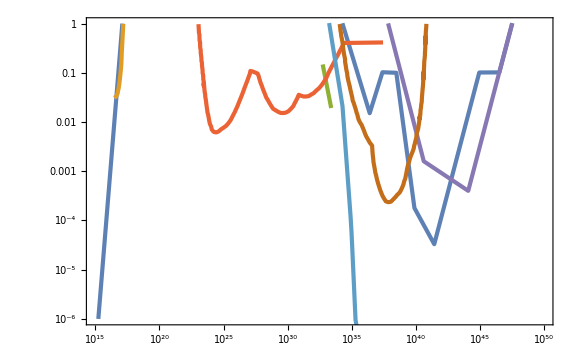

```mathematica
Show[LogLogPlot[fEGB[M],{M,10^15,10^50},PlotRange->{10^-6,1}],ListLogLogPlot[{DF,GC,GW,lensing,LSS,XB,PA}]]
```

## const on power

### DM

```mathematica
gsdata=Import["gs_dof.dat"];
```

```mathematica
gList=Map[{#[[1]],#[[2]]}&,gsdata];
gint[T_]=Interpolation[gList][T];
```

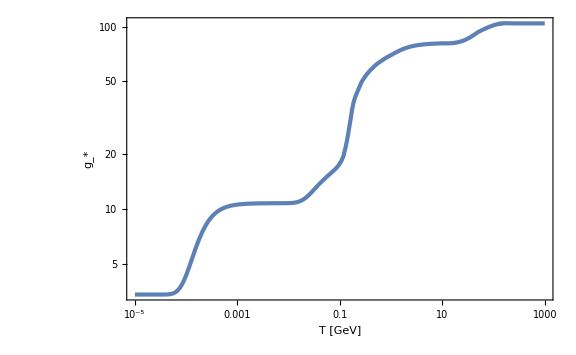

```mathematica
LogLogPlot[gint[T],{T,10^-5,10^3},FrameLabel->{"T [GeV]",SubStar[g]}]
```

```mathematica
KinGeV=10^-9/(1.160 10^4);
Omh2=0.143;
aeq=1/(2.4 10^4 Omh2);
keq=0.07Omh2;
Teq=(2.725KinGeV)/aeq
geq=3.38;
kinT[T_]=keq 2(Sqrt[2]-1)(gint[T]/geq)^(1/6)T/Teq;
```

8.06224×10^-10

```mathematica
kinT[10^-9]
```

0.0102872

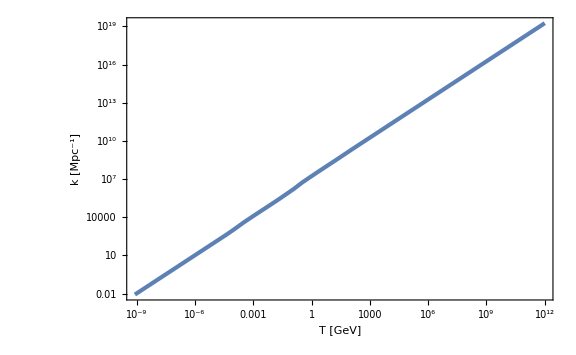

```mathematica
LogLogPlot[kinT[T],{T,Teq,10^12},FrameLabel->{"T [GeV]","k [Mpc^-1]"}]
```

```mathematica
T20=T/.FindRoot[kinT[T]==1.56 10^13,{T,10^5}]
```

856114.

```mathematica
muinM[MoMk_]=FullSimplify[mu/.Solve[MoMk==xm^2 E^(2mu Sin[xm]/xm)(mu-muth)^γ,mu][[1]],{γ>0,xm>0}]/.{muth->0.615,xm->2.74,γ->0.36}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.615+1.26175 ProductLog[0.00180051 MoMk^2.77778]

```mathematica
f[xi_]=1/2 xi(xi^2-3)(Erf[1/2 Sqrt[5/2]xi]+Erf[Sqrt[5/2]xi])+Sqrt[2/(5π)]((8/5+31/4 xi^2)Exp[-5/8 xi^2]+(-8/5+1/2 xi^2)Exp[-5/2 xi^2]);
PG[x_,A_]=1/Sqrt[2π A] Exp[-x^2/(2A)];
```

```mathematica
dlnMdmu[mu_]=0.282+0.36/(mu-0.615);
```

```mathematica
fPBH[MoMk_,A_,T_]=MoMk (gint[T]/106.75)^(-1/6)kinT[T]/(1.56 10^13)(dlnMdmu[muinM[MoMk]]^-1 f[muinM[MoMk]/Sqrt[A]]PG[muinM[MoMk],A])/(5.3 10^-16);
```

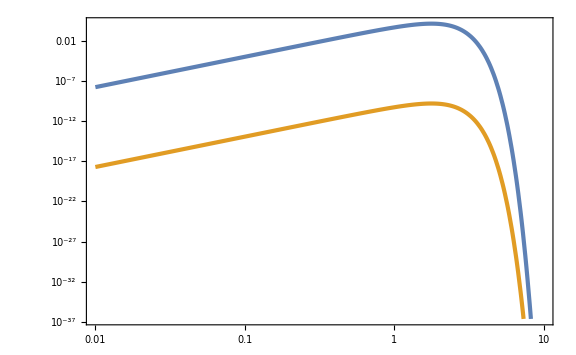

```mathematica
LogLogPlot[{fPBH[MoMk,4.863 10^-3,T20],fPBH[MoMk,4.863 10^-3,10^-4]},{MoMk,10^-2,10}]
```

```mathematica
NIntegrate[fPBH[MoMk,4.863 10^-3,T20]/MoMk,{MoMk,10^-2,5}]
```

1.05463

```mathematica
fM[MoMk_,A_]=(dlnMdmu[muinM[MoMk]]^-1 f[muinM[MoMk]/Sqrt[A]]PG[muinM[MoMk],A])/(5.3 10^-16);
```

```mathematica
NIntegrate[fM[MoMk,10^0],{MoMk,10^-2,5}]
```

1.49965×10^12

```mathematica
fMintegList=Table[{10^lnA,NIntegrate[fM[MoMk,10^lnA],{MoMk,10^-2,5}]},{lnA,-3,0,1/100}];
```

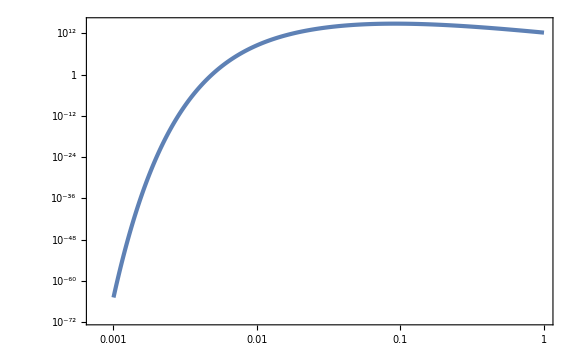

```mathematica
ListLogLogPlot[fMintegList]
```

```mathematica
fMint[A_]=Interpolation[fMintegList][A];
```

```mathematica
fMmax=FindMaximum[fMint[A],{A,0.09}][[1]]
Amax=A/.FindMaximum[fMint[A],{A,0.09}][[2]]
```

6.08364×10^14

0.0911834

```mathematica
Tmin=T/.FindRoot[(gint[T]/106.75)^(-1/6)kinT[T]/(1.56 10^13)fMmax==1,{T,10^-8}]
```

1.40223×10^-9

```mathematica
FindRoot[(gint[Tmin]/106.75)^(-1/6)kinT[Tmin]/(1.56 10^13)fMint[A]==1,{A,10^-2,10^-3,Amax}]
```

FindRoot::reged: The point {0.0911834} is at the edge of the search region {0.001,0.0911834} in coordinate 1 and the computed search direction points outside the region.

{A→0.0911834}

```mathematica
AconstDM=Table[{kinT[10^lnT],A/.FindRoot[(gint[10^lnT]/106.75)^(-1/6)kinT[10^lnT]/(1.56 10^13)fMint[A]==1,{A,10^-2,10^-3,Amax}]},{lnT,Log10[Tmin],12,1/100}];
```

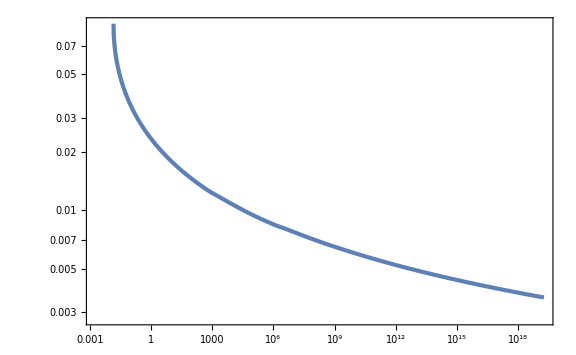

```mathematica
ListLogLogPlot[AconstDM]
```

```mathematica
Msol=1.988 10^33;
```

```mathematica
MinT[T_]=10^20(gint[T]/106.75)^(-1/6)(kinT[T]/(1.56 10^13))^-2;
```

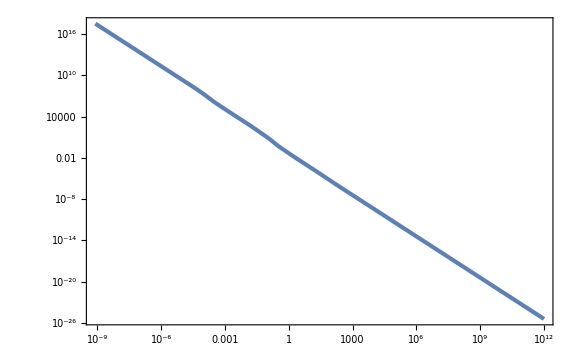

```mathematica
LogLogPlot[MinT[T]/Msol,{T,Teq,10^12}]
```

```mathematica
Export["AconstDM.dat",AconstDM];
```

### EGB

```mathematica
Ms=5 10^14;
fEGB[M_]=2 10^-8(M/Ms)^3.2;
MminEGB=2Ms;
MmaxEGB=(2 10^-8)^(-1/3.2)Ms
TminEGB=T/.FindRoot[10^-2 MinT[T]==MmaxEGB,{T,1}]
TmaxEGB=T/.FindRoot[5MinT[T]==MminEGB,{T,1}]
```

1.2732×10^17

2.40329×10^6

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

6.0604×10^8

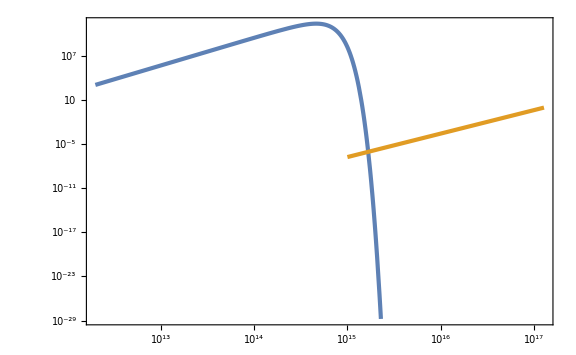

```mathematica
LogLogPlot[{fPBH[M/MinT[TmaxEGB],10^-2,TmaxEGB],fEGB[M]UnitStep[M-MminEGB]},{M,10^-2 MinT[TmaxEGB],MmaxEGB}]
```

```mathematica
Ts=TmaxEGB E^(-1/1000);
NIntegrate[fPBH[M/MinT[Ts],10^-2,Ts]/(fEGB[M]M),{M,Max[10^-2 MinT[Ts],MminEGB],Min[5MinT[Ts],MmaxEGB]}]
```

1.91343×10^12

```mathematica
ftotEGBList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fEGB[M]M),{M,Max[10^-2 MinT[10^lnT],MminEGB],Min[5MinT[10^lnT],MmaxEGB]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminEGB],Log10[TmaxEGB],1/100},{lnA,-3,-2,1/100}],1];//AbsoluteTiming
```

{103.556,Null}

```mathematica
ftotEGBint[k_,A_]=Interpolation[ftotEGBList,InterpolationOrder->1][k,A]
```

InterpolatingFunction[…][k,A]

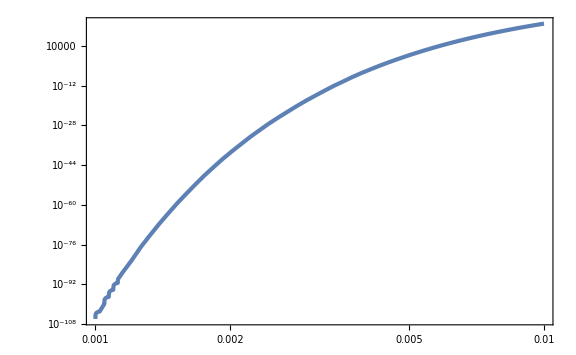

```mathematica
LogLogPlot[ftotEGBint[1.1005055258039372*^16,A],{A,10^-3,10^-2}]
```

```mathematica
FindRoot[ftotEGBint[kinT[TminEGB],A]==1,{A,5 10^-3}]
```

InterpolatingFunction::dmval: Input value {4.37959×10^13,10.055} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.37959×10^13,5.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.37959×10^13,2.5175} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{A→0.005}

```mathematica
AconstEGB=Table[{10^lnk,A/.FindRoot[ftotEGBint[10^lnk,A]==1,{A,5 10^-3}]},{lnk,Log10[kinT[TminEGB]]+1/100,Log10[kinT[TmaxEGB]],1/100}];
```

InterpolatingFunction::dmval: Input value {4.4816×10^13,10.055} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.4816×10^13,1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.4816×10^13,0.5075} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

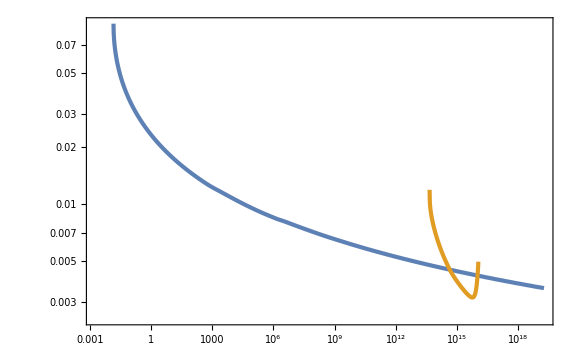

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB}]
```

```mathematica
Export["AconstEGB.dat",AconstEGB];
```

### GC

```mathematica
GCdata=Import["PBHconstFlo/GC.csv"];
```

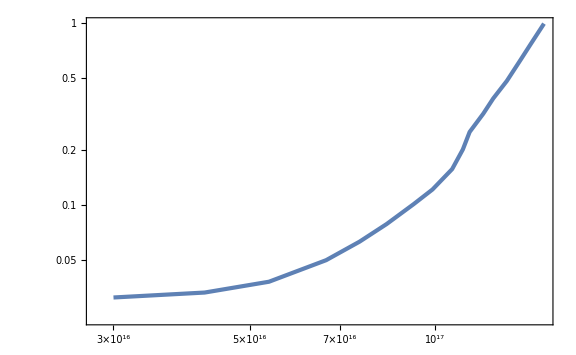

```mathematica
ListLogLogPlot[GCdata]
```

```mathematica
fGC[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,GCdata],InterpolationOrder->1][Log[M]]];
MminGC=First[GCdata][[1]];
MmaxGC=Last[GCdata][[1]];
TminGC=T/.FindRoot[10^-2 MinT[T]==MmaxGC,{T,1},WorkingPrecision->30]
TmaxGC=T/.FindRoot[5MinT[T]==MminGC,{T,1},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ((7.51884×10^30)/(T^2 «1»)==150375931207794500) is less than WorkingPrecision (30.).

2.21141822822843462635830294042×10^6

FindRoot::precw: The precision of the argument function ((3.75942×10^33)/(T^2 «1»)==30010290183980988) is less than WorkingPrecision (30.).

1.10645714035065535972382535988×10^8

```mathematica
Max[10^-2 MinT[TminGC],MminGC]
Min[5MinT[TminGC],MmaxGC]
Max[10^-2 MinT[TmaxGC],MminGC]
Min[5MinT[TmaxGC],MmaxGC]
```

1.50376×10^17

150375931207794500

30010290183980988

3.00103×10^16

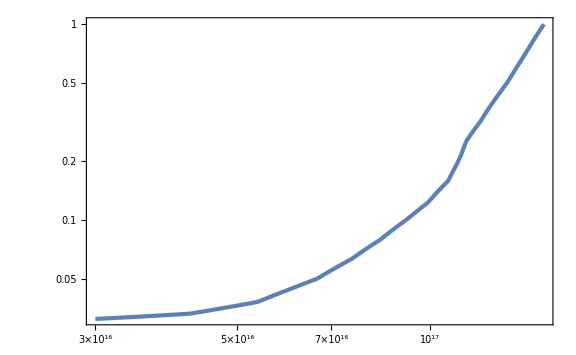

```mathematica
LogLogPlot[fGC[M],{M,MminGC,MmaxGC}]
```

```mathematica
ftotGCList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fGC[M]M),{M,Max[10^-2 MinT[10^lnT],MminGC],Min[5MinT[10^lnT],MmaxGC]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminGC],Log10[TmaxGC],1/100},{lnA,-3,-2,1/100}],1];//AbsoluteTiming
```

{638.183,Null}

```mathematica
Export["ftotGC.dat",ftotGCList];
```

```mathematica
ftotGCint[k_,A_]=Interpolation[ftotGCList,InterpolationOrder->1][k,A];
```

```mathematica
AconstGC=Table[{10^lnk,A/.FindRoot[ftotGCint[10^lnk,A]==1,{A,5 10^-3}]},{lnk,Log10[kinT[TminGC]]+1/100,Log10[kinT[TmaxGC]],1/100}];
```

InterpolatingFunction::dmval: Input value {4.12377×10^13,10.055} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.12377×10^13,1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.12377×10^13,0.5075} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

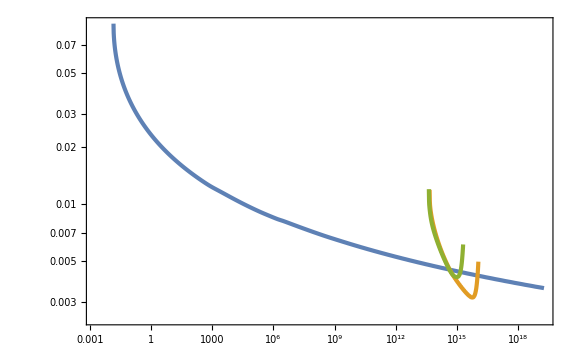

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC}]
```

```mathematica
AconstEGBint[k_]=Interpolation[AconstEGB][k];
AconstGCint[k_]=Interpolation[AconstGC][k];
```

```mathematica
AconstEvap[k_]=Min[AconstEGBint[k],AconstGCint[k]];
```

InterpolatingFunction::dmval: Input value {4.12424×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

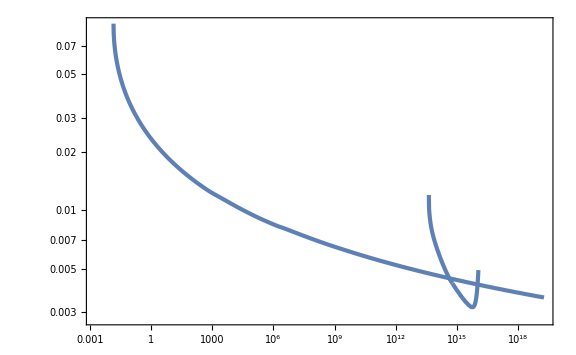

```mathematica
Show[ListLogLogPlot[AconstDM],LogLogPlot[AconstEvap[k],{k,First[AconstGC][[1]],Last[AconstEGB][[1]]}]]
```

```mathematica
Export["AconstGC.dat",AconstGC];
```

### lensing

```mathematica
Lensdata=Import["PBHconstFlo/lensing.csv"];
```

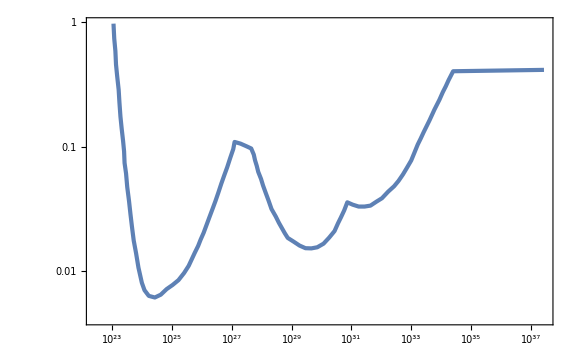

```mathematica
ListLogLogPlot[Lensdata]
```

```mathematica
fLens[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,Lensdata],InterpolationOrder->1][Log[M]]];
MminLens=First[Lensdata][[1]]
MmaxLens=Last[Lensdata][[1]]
TminLens=T/.FindRoot[10^-2 MinT[T]==MmaxLens,{T,10^-4}]
TmaxLens=T/.FindRoot[5MinT[T]==MminLens,{T,1}]
```

1.1124×10^23

2.77786×10^37

0.000301243

57517.

```mathematica
ftotLensList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fLens[M]M),{M,Max[10^-2 MinT[10^lnT],MminLens],Min[5MinT[10^lnT],MmaxLens]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminLens],Log10[TmaxLens],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{6066.36,Null}

```mathematica
Export["ftotLens.dat",ftotLensList];
```

```mathematica
ftotLensint[k_,A_]=Interpolation[ftotLensList,InterpolationOrder->1][k,A];
```

```mathematica
kinT[TminLens]
kinT[TmaxLens]
```

3640.82

1.04785×10^12

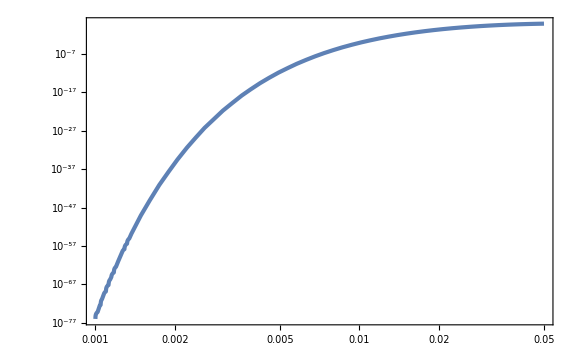

```mathematica
LogLogPlot[ftotLensint[1.5 10^4,A],{A,10^-3,5 10^-2}]
```

```mathematica
AconstLens=Select[Table[{10^lnk,If[ftotLensint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotLensint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminLens]]+1/100,Log10[kinT[TmaxLens]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {3725.62,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3812.4,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3901.21,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

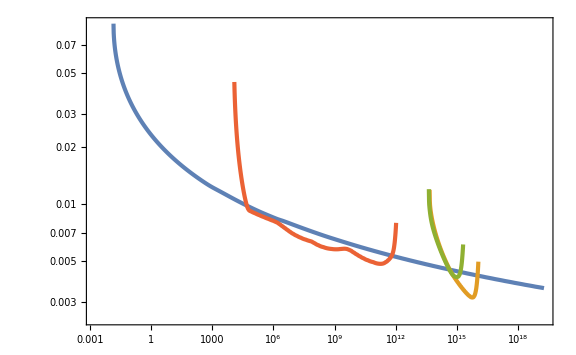

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens}]
```

```mathematica
Export["AconstLens.dat",AconstLens];
```

### XB

```mathematica
XBdata=Import["PBHconstFlo/XB.csv"];
```

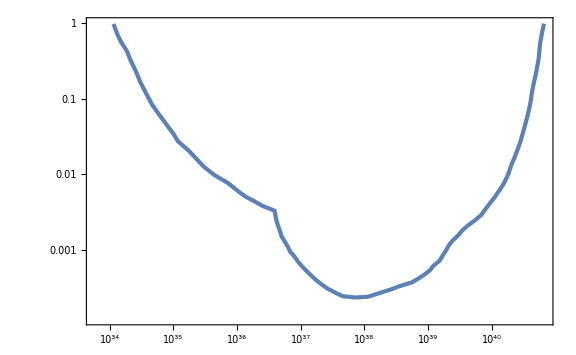

```mathematica
ListLogLogPlot[XBdata]
```

```mathematica
fXB[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,XBdata],InterpolationOrder->1][Log[M]]];
MminXB=First[XBdata][[1]]
MmaxXB=Last[XBdata][[1]]
TminXB=T/.FindRoot[10^-2 MinT[T]==MmaxXB,{T,10^-5},WorkingPrecision->30]
TmaxXB=T/.FindRoot[5MinT[T]==MminXB,{T,0.1},WorkingPrecision->30]
```

1.15276×10^34

6.6739×10^40

FindRoot::precw: The precision of the argument function ((7.51884×10^30)/(T^2 «1»)==6.6739×10^40) is less than WorkingPrecision (30.).

7.8263140037739454902649771088×10^-6

FindRoot::precw: The precision of the argument function ((3.75942×10^33)/(T^2 «1»)==1.15276×10^34) is less than WorkingPrecision (30.).

0.221554372736804482203110374783

```mathematica
ftotXBList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fXB[M]M),{M,Max[10^-2 MinT[10^lnT],MminXB],Min[5MinT[10^lnT],MmaxXB]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminXB],Log10[TmaxXB],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{4816.01,Null}

```mathematica
Export["ftotXB.dat",ftotXBList];
```

```mathematica
ftotXBint[k_,A_]=Interpolation[ftotXBList,InterpolationOrder->1][k,A];
```

```mathematica
AconstXB=Select[Table[{10^lnk,If[ftotXBint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotXBint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminXB]]+1/100,Log10[kinT[TmaxXB]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {82.3865,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {84.3055,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {86.2692,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

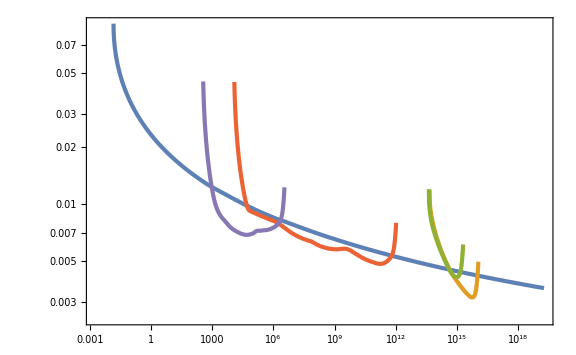

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB}]
```

```mathematica
Export["AconstXB.dat",AconstXB];
```

### DF

```mathematica
DFdata=Import["PBHconstFlo/DF.csv"];
```

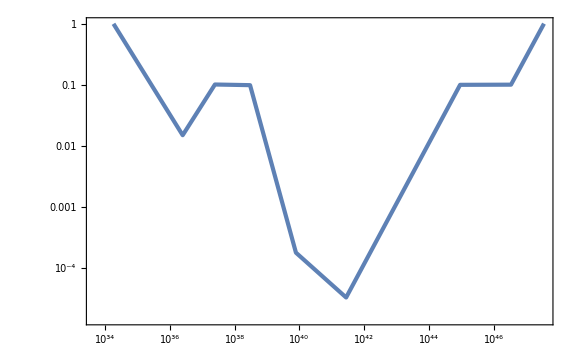

```mathematica
ListLogLogPlot[DFdata]
```

```mathematica
fDF[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,DFdata],InterpolationOrder->1][Log[M]]];
MminDF=First[DFdata][[1]]
MmaxDF=Last[DFdata][[1]]
TminDF=T/.FindRoot[10^-2 MinT[T]==MmaxDF,{T,3 10^-9},WorkingPrecision->30]
TmaxDF=T/.FindRoot[5MinT[T]==MminDF,{T,0.3},WorkingPrecision->30]
```

1.8669×10^34

3.42382×10^47

FindRoot::precw: The precision of the argument function ((7.51884×10^30)/(T^2 «1»)==3.42382×10^47) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {3.×10^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.36929175709962353909950527665×10^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45215842584578587608069435388×10^-9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.4553465037535503221650246636×10^-9

FindRoot::precw: The precision of the argument function ((3.75942×10^33)/(T^2 «1»)==1.8669×10^34) is less than WorkingPrecision (30.).

0.18164272831255424483437449764

```mathematica
10^-2 MinT[TminDF]
MmaxDF
```

3.42382×10^47

3.42382×10^47

```mathematica
ftotDFList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fDF[M]M),{M,Max[10^-2 MinT[10^lnT],MminDF],Min[5MinT[10^lnT],MmaxDF]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminDF],Log10[TmaxDF],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{713.819,Null}

```mathematica
Export["ftotDF.dat",ftotDFList];
```

```mathematica
ftotDFint[k_,A_]=Interpolation[ftotDFList,InterpolationOrder->1][k,A];
```

```mathematica
AconstDF=Select[Table[{10^lnk,If[ftotDFint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotDFint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminDF]]+1/100,Log10[kinT[TmaxDF]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {0.0363739,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0372212,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0380882,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

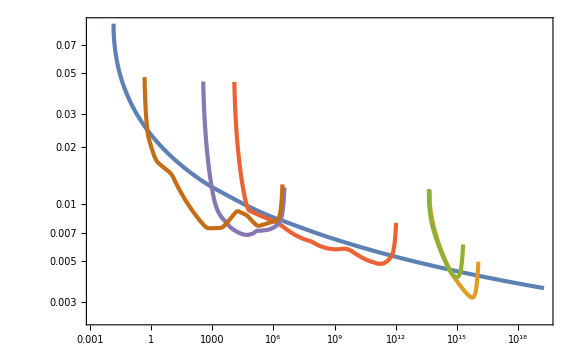

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB,AconstDF}]
```

```mathematica
Export["AconstDF.dat",AconstDF];
```

### LSS

```mathematica
LSSdata=Import["PBHconstFlo/LSS.csv"];
```

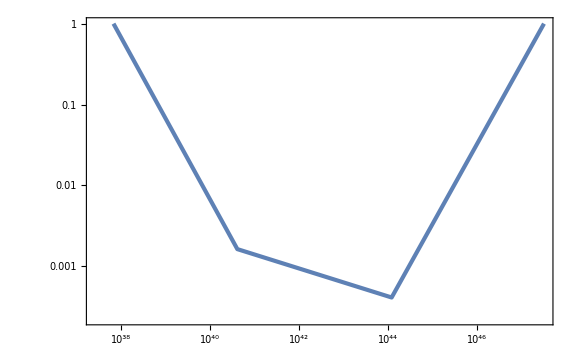

```mathematica
ListLogLogPlot[LSSdata]
```

```mathematica
fLSS[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,LSSdata],InterpolationOrder->1][Log[M]]];
MminLSS=First[LSSdata][[1]]
MmaxLSS=Last[LSSdata][[1]]
TminLSS=T/.FindRoot[10^-2 MinT[T]==MmaxLSS,{T,10^-10}]
TmaxLSS=T/.FindRoot[5MinT[T]==MminLSS,{T,10^-5},WorkingPrecision->30]
```

6.88987×10^37

3.25405×10^47

3.54434×10^-9

FindRoot::precw: The precision of the argument function ((3.75942×10^33)/(T^2 «1»)==6.88987×10^37) is less than WorkingPrecision (30.).

0.00408192485444014331901681190265

```mathematica
ftotLSSList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fLSS[M]M),{M,Max[10^-2 MinT[10^lnT],MminLSS],Min[5MinT[10^lnT],MmaxLSS]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminLSS],Log10[TmaxLSS],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{507.885,Null}

```mathematica
Export["ftotLSS.dat",ftotLSSList];
```

```mathematica
ftotLSSint[k_,A_]=Interpolation[ftotLSSList,InterpolationOrder->1][k,A];
```

```mathematica
AconstLSS=Select[Table[{10^lnk,If[ftotLSSint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotLSSint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminLSS]]+1/100,Log10[kinT[TmaxLSS]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {0.0373107,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0381798,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0390691,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

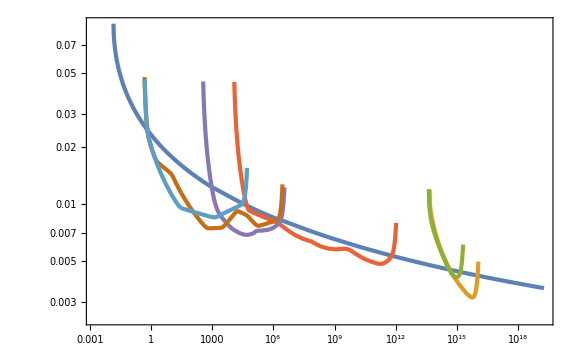

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB,AconstDF,AconstLSS}]
```

```mathematica
Export["AconstLSS.dat",AconstLSS];
```

### PA

```mathematica
PAdata=Import["PBHconstFlo/PA.csv"];
```

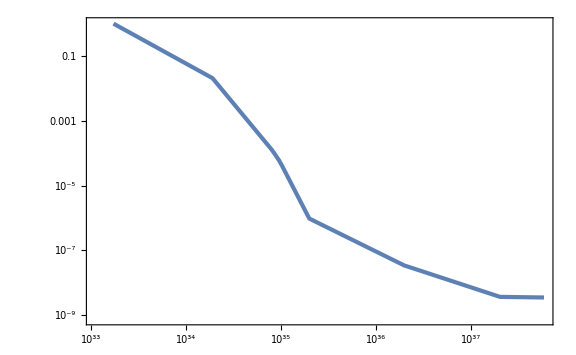

```mathematica
ListLogLogPlot[PAdata]
```

```mathematica
fPA[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,PAdata],InterpolationOrder->1][Log[M]]];
MminPA=First[PAdata][[1]]
MmaxPA=Last[PAdata][[1]]
TminPA=T/.FindRoot[10^-2 MinT[T]==MmaxPA,{T,0.0002},WorkingPrecision->30]
TmaxPA=T/.FindRoot[5MinT[T]==MminPA,{T,0.5},WorkingPrecision->30]
```

1.72808×10^33

5.86731×10^37

FindRoot::precw: The precision of the argument function ((7.51884×10^30)/(T^2 «1»)==5.86731×10^37) is less than WorkingPrecision (30.).

0.000215300903401378732633484544171

FindRoot::precw: The precision of the argument function ((3.75942×10^33)/(T^2 «1»)==1.72808×10^33) is less than WorkingPrecision (30.).

0.525173398319058906265865069692

```mathematica
ftotPAList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fPA[M]M),{M,Max[10^-2 MinT[10^lnT],MminPA],Min[5MinT[10^lnT],MmaxPA]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminPA],Log10[TmaxPA],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{310.446,Null}

```mathematica
Export["ftotPA.dat",ftotPAList];
```

```mathematica
ftotPAint[k_,A_]=Interpolation[ftotPAList,InterpolationOrder->1][k,A];
```

```mathematica
AconstPA=Select[Table[{10^lnk,If[ftotPAint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotPAint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminPA]]+1/100,Log10[kinT[TmaxPA]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {2596.17,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2596.17,0.110348} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2656.64,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

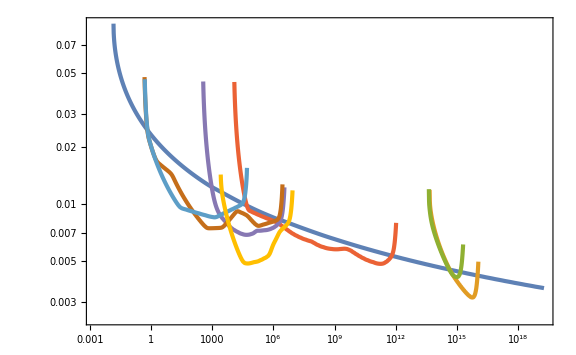

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB,AconstDF,AconstLSS,AconstPA}]
```

```mathematica
Export["AconstPA.dat",AconstPA];
```

### GW

```mathematica
GWdata=Import["PBHconstFlo/GW.csv"];
```

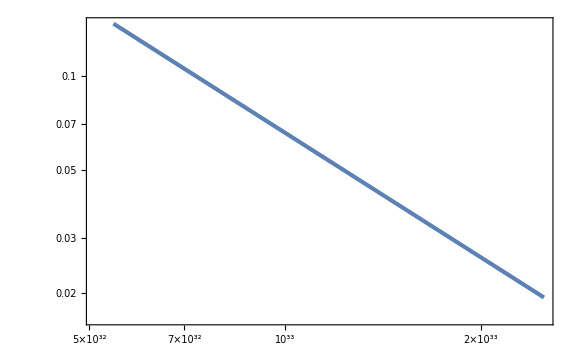

```mathematica
ListLogLogPlot[GWdata]
```

```mathematica
fGW[M_]=Exp[Interpolation[Map[{Log[#[[1]]],Log[#[[2]]]}&,GWdata],InterpolationOrder->1][Log[M]]];
MminGW=First[GWdata][[1]]
MmaxGW=Last[GWdata][[1]]
TminGW=T/.FindRoot[10^-2 MinT[T]==MmaxGW,{T,10^-2},WorkingPrecision->30]
TmaxGW=T/.FindRoot[5MinT[T]==MminGW,{T,1}]
```

5.44575×10^32

2.50423×10^33

FindRoot::precw: The precision of the argument function ((7.51884×10^30)/(T^2 «1»)==2.50423×10^33) is less than WorkingPrecision (30.).

0.0291634481546841522504041791881

0.91214

```mathematica
ftotGWList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fGW[M]M),{M,Max[10^-2 MinT[10^lnT],MminGW],Min[5MinT[10^lnT],MmaxGW]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminGW],Log10[TmaxGW],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{105.299,Null}

```mathematica
Export["ftotGW.dat",ftotGWList];
```

```mathematica
ftotGWint[k_,A_]=Interpolation[ftotGWList,InterpolationOrder->1][k,A];
```

```mathematica
AconstGW=Select[Table[{10^lnk,If[ftotGWint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotGWint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminGW]]+1/100,Log10[kinT[TmaxGW]]-1/100,1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {381521.,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {390407.,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {399501.,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["AconstGW.dat",AconstGW];
```

```mathematica
AconstDM=Import["AconstDM.dat"];
AconstEGB=Import["AconstEGB.dat"];
AconstGC=Import["AconstGC.dat"];
AconstLens=Import["AconstLens.dat"];
AconstXB=Import["AconstXB.dat"];
AconstDF=Import["AconstDF.dat"];
AconstLSS=Import["AconstLSS.dat"];
AconstPA=Import["AconstPA.dat"];
AconstGW=Import["AconstGW.dat"];
```

```mathematica
AconstEGBint[k_]=Interpolation[AconstEGB][k];
AconstGCint[k_]=Interpolation[AconstGC][k];
```

```mathematica
AconstEvap[k_]=Min[AconstEGBint[k],AconstGCint[k]];
```

```mathematica
EvapC=RGBColor["#FF0000"];
LensC=RGBColor["#0000FF"];
XBC=RGBColor["#00AAAA"];
DFC=RGBColor["#00AA00"];
LSSC=RGBColor["#FFB3FF"];
PAC=RGBColor["#FFAA55"];
GWC=RGBColor["#AAAAAA"];
```

```mathematica
MHticks=
Table[If[i==-20||i==-10||i==10||i==20,{kinT[10^logT]/.FindRoot[MinT[10^logT]==10^i Msol,{logT,-i/2}],10^ToString[i],{0.01,0}},If[i==0,{kinT[10^logT]/.FindRoot[MinT[10^logT]==10^i Msol,{logT,0}],1,{0.01,0}},{kinT[10^logT]/.FindRoot[MinT[10^logT]==10^i Msol,{logT,-i/2}],"",{0.005,0}}]],{i,-24,20,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{3.50371×10^18,,{0.005,0}},{3.50391×10^17,,{0.005,0}},{3.50412×10^16,10^-20,{0.01,0}},{3.50436×10^15,,{0.005,0}},{3.50463×10^14,,{0.005,0}},{3.50491×10^13,,{0.005,0}},{3.50522×10^12,,{0.005,0}},{3.50553×10^11,10^-10,{0.01,0}},{3.50583×10^10,,{0.005,0}},{3.50545×10^9,,{0.005,0}},{3.57594×10^8,,{0.005,0}},{3.59617×10^7,,{0.005,0}},{3.75272×10^6,1,{0.01,0}},{417307.,,{0.005,0}},{42374.1,,{0.005,0}},{4286.77,,{0.005,0}},{466.374,,{0.005,0}},{46.6485,10^10,{0.01,0}},{4.66485,,{0.005,0}},{0.466485,,{0.005,0}},{0.0466485,,{0.005,0}},{0.00466485,,{0.005,0}},{0.000466485,10^20,{0.01,0}}}

InterpolatingFunction::dmval: Input value {4.12424×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

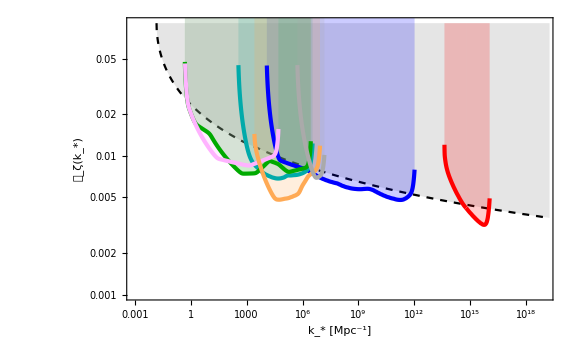

```mathematica
PconstPBH=Show[ListLogLogPlot[AconstDM,FrameLabel->{{Subscript[𝒫, ζ][SubStar[k]],None},{"k_* [Mpc^-1]",Row[{Subscript[M, H][SubStar[k]]," / ",M_☉}]}},PlotStyle->{Black,Dashed},Filling->Top,PlotRange->{{10^-3,10^19},{0.001,0.09}},FillingStyle->Directive[Opacity[0.1]],FrameTicks->{Automatic,{Automatic,MHticks}}],ListLogLogPlot[{AconstLens,AconstXB,AconstDF,AconstLSS,AconstPA,AconstGW},Filling->Top,PlotRange->{0.001,0.9},PlotStyle->{{AbsoluteThickness[3],LensC},{AbsoluteThickness[3],XBC},{AbsoluteThickness[3],DFC},{AbsoluteThickness[3],LSSC},{AbsoluteThickness[3],PAC},{AbsoluteThickness[3],GWC}}],LogLogPlot[AconstEvap[k],{k,First[AconstGC][[1]],Last[AconstEGB][[1]]},Filling->Top,PlotRange->{0.001,0.09},PlotStyle->{AbsoluteThickness[3],EvapC}]]
```

```mathematica
AconstEvapList=Table[{10^lnk,AconstEvap[10^lnk]},{lnk,Log10[First[AconstGC][[1]]],Log10[Last[AconstEGB][[1]]],10^-2}];
```

InterpolatingFunction::dmval: Input value {4.12377×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.21982×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.31812×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Export["AconstEvap.dat",AconstEvapList];
```

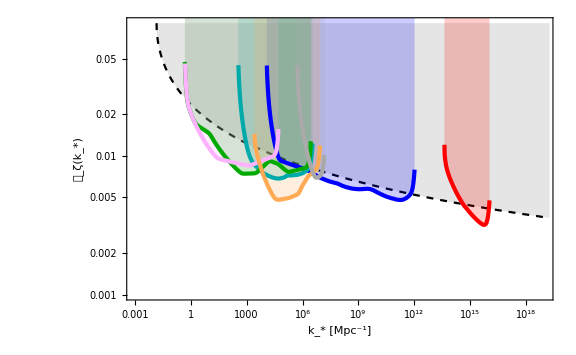

```mathematica
PconstPBH=Show[ListLogLogPlot[AconstDM,FrameLabel->{{Subscript[𝒫, ζ][SubStar[k]],None},{"k_* [Mpc^-1]",Row[{Subscript[M, H][SubStar[k]]," / ",M_☉}]}},PlotStyle->{Black,Dashed},Filling->Top,PlotRange->{{10^-3,10^19},{0.001,0.09}},FillingStyle->Directive[Opacity[0.1]],FrameTicks->{Automatic,{Automatic,MHticks}}],ListLogLogPlot[{AconstLens,AconstXB,AconstDF,AconstLSS,AconstPA,AconstGW,AconstEvapList},Filling->Top,PlotRange->{0.001,0.9},PlotStyle->{{AbsoluteThickness[3],LensC},{AbsoluteThickness[3],XBC},{AbsoluteThickness[3],DFC},{AbsoluteThickness[3],LSSC},{AbsoluteThickness[3],PAC},{AbsoluteThickness[3],GWC},{AbsoluteThickness[3],EvapC}}](*,LogLogPlot[AconstEvap[k],{k,First[AconstGC][[1]],Last[AconstEGB][[1]]},Filling->Top,PlotRange->{0.001,0.09},PlotStyle->{AbsoluteThickness[3],EvapC}]*)]
```